```mathematica
Import["/Users/miaanand/Downloads/download.json", "Data"]//Normal
```

```mathematica
Values[%210][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]][[1]]
```

{value→579.09,qualifiers→{P},dateTime→2023-07-25T09:48:00.000-05:00}

```mathematica
Table[Values[%210][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]][[n]][[1]][[2]], {n,1,Length[Values[%210][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]][[1]]]}]
```

{579.09,579.06,579.04}

```mathematica
levels =ToExpression/@Table[Values[%210][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]][[n]][[1]][[2]], {n,1,832}];
```

```mathematica
Last[Sort[%306]]
```

579.52

```mathematica
Head@%
```

Real

```mathematica
divideSequence = Select[N/@Table[1/(Last[Sort[levels]]/levels[[i]]), {i,1,Length[levels]}], LessThan[1]]
```

{0.999258,0.999206,0.999172,0.999154,0.999154,0.999172,0.999189,0.999206,0.999189,0.999154,0.999137,0.99912,0.999103,0.99912,0.999154,0.999154,0.999189,0.999189,0.999154,0.999137,0.99912,0.999172,0.999189,0.999189,0.999154,0.999154,0.999154,0.999137,0.99912,0.999137,0.999137,0.999137,0.999154,0.999189,0.999172,0.999154,0.999154,0.999189,0.999189,0.999172,0.999137,0.999103,0.999103,0.999085,0.999085,0.99912,0.999172,0.999223,0.999206,0.999189,0.999137,0.999103,0.999085,0.99912,0.999154,0.999172,0.999172,0.999172,0.999172,0.999154,0.99912,0.999103,0.999085,0.999085,0.999068,0.999034,0.999016,0.999034,0.999103,0.999206,0.999189,0.99912,0.999085,0.999051,0.999068,0.999034,0.998999,0.998999,0.998999,0.998999,0.998947,0.998965,0.998999,0.999085,0.999103,0.999085,0.999085,0.999068,0.999085,0.999103,0.99912,0.999137,0.999103,0.999085,0.999068,0.999085,0.999068,0.999085,0.999085,0.999068,0.999103,0.999085,0.999068,0.999068,0.999085,0.999085,0.999051,0.999016,0.999016,0.999016,0.999034,0.999034,0.999034,0.999016,0.999051,0.999103,0.999085,0.999085,0.999085,0.999103,0.999085,0.999068,0.999034,0.999016,0.999016,0.999016,0.998982,0.998999,0.998999,0.999016,0.999068,0.999085,0.999034,0.999016,0.999051,0.999051,0.998999,0.998947,0.998947,0.998913,0.998896,0.998896,0.99893,0.998965,0.998982,0.998965,0.998913,0.998913,0.99893,0.998947,0.998947,0.998982,0.999051,0.999051,0.998999,0.998913,0.998861,0.998861,0.998947,0.999034,0.999154,0.999206,0.999189,0.999172,0.999189,0.99931,0.999413,0.999448,0.999379,0.999275,0.999154,0.998999,0.99893,0.998999,0.999085,0.999085,0.99912,0.999241,0.999327,0.999362,0.999327,0.999275,0.999258,0.99931,0.999327,0.999241,0.999172,0.999154,0.999172,0.999137,0.999172,0.999258,0.999344,0.99931,0.999206,0.99912,0.999085,0.999172,0.999275,0.99931,0.999327,0.999344,0.999362,0.999327,0.999241,0.999172,0.999172,0.999275,0.999344,0.999379,0.999344,0.999327,0.999379,0.999448,0.999413,0.999362,0.999344,0.999379,0.999413,0.999448,0.999413,0.999396,0.999344,0.999362,0.999413,0.999534,0.999603,0.99962,0.99962,0.99962,0.999586,0.9995,0.999413,0.999344,0.99931,0.999258,0.999189,0.999172,0.999154,0.999154,0.99912,0.999172,0.999241,0.999293,0.99931,0.999293,0.99931,0.999258,0.999206,0.999206,0.999241,0.99931,0.999293,0.999327,0.999327,0.999344,0.999413,0.999517,0.99962,0.999707,0.999655,0.999534,0.999396,0.999258,0.999154,0.999085,0.999085,0.999154,0.999241,0.999241,0.999189,0.999154,0.99912,0.999137,0.999154,0.999172,0.99912,0.999051,0.998965,0.998982,0.999085,0.99912,0.999068,0.999085,0.999189,0.99931,0.999396,0.9995,0.999655,0.999845,0.999793,0.999689,0.999586,0.999448,0.99931,0.999189,0.999206,0.999241,0.999275,0.999327,0.999275,0.999206,0.999206,0.999223,0.999189,0.999137,0.999051,0.998982,0.99893,0.998982,0.999068,0.999068,0.999034,0.999034,0.999103,0.999206,0.999327,0.999379,0.999362,0.999344,0.999362,0.99931,0.999275,0.999275,0.99931,0.999362,0.999379,0.999379,0.999362,0.999275,0.999189,0.999137,0.999051,0.998982,0.998982,0.999016,0.999034,0.999051,0.99912,0.999223,0.999189,0.999068,0.998947,0.998913,0.998913,0.998896,0.998878,0.99893,0.999051,0.999172,0.999275,0.999362,0.999413,0.9995,0.999586,0.999603,0.999517,0.999448,0.999362,0.999275,0.999241,0.999293,0.999362,0.999344,0.999379,0.999431,0.999482,0.999431,0.999362,0.999293,0.999172,0.999051,0.998965,0.998896,0.998878,0.998965,0.999051,0.999154,0.999275,0.999344,0.999344,0.999344,0.999379,0.999431,0.9995,0.999517,0.999534,0.999551,0.999672,0.999965,0.999793,0.999551,0.999379,0.999396,0.999413,0.999379,0.999344,0.999241,0.99912,0.999085,0.99912,0.999189,0.999258,0.999241,0.999223,0.999223,0.999137,0.999068,0.999103,0.999154,0.999206,0.999241,0.999241,0.999293,0.999396,0.999482,0.999517,0.999448,0.999396,0.999362,0.999344,0.99931,0.999293,0.99931,0.999344,0.999431,0.999396,0.999275,0.999206,0.999293,0.999362,0.999293,0.99931,0.999327,0.999431,0.999413,0.999344,0.999293,0.999344,0.999362,0.99931,0.999206,0.999655,0.99962,0.999517,0.999431,0.999362,0.999275,0.999258,0.999362,0.999482,0.999517,0.999551,0.999586,0.999586,0.999569,0.9995,0.9995,0.999586,0.99962,0.999586,0.999534,0.999482,0.999431,0.999465,0.999534,0.999569,0.999517,0.9995,0.999586,0.999672,0.999689,0.999638,0.999586,0.99962,0.99962,0.999586,0.999586,0.999569,0.999586,0.99962,0.999638,0.999689,0.999758,0.99981,0.999931,0.999965,0.999896,0.999896,0.999965,0.999931,0.999845,0.999724,0.99962,0.999517,0.999517,0.999551,0.99962,0.999655,0.999569,0.999448,0.99931,0.999189,0.999103,0.999085,0.99912,0.999206,0.99931,0.999431,0.999517,0.999517,0.999482,0.999413,0.999327,0.999241,0.999154,0.999154,0.999189,0.999293,0.999413,0.999465,0.999431,0.999396,0.999344,0.999275,0.999206,0.99912,0.999085,0.999103,0.999137,0.999206,0.999241,0.999327,0.999379,0.999413,0.999413,0.999396,0.999413,0.999465,0.9995,0.999431,0.999344,0.999275,0.99931,0.999344,0.999275,0.99931,0.999413,0.999534,0.999569,0.999534,0.9995,0.999465,0.999431,0.999362,0.999379,0.999379,0.999431,0.999482,0.999534,0.999534,0.999534,0.999465,0.999413,0.999431,0.999431,0.999431,0.999379,0.99931,0.999293,0.999327,0.999362,0.999362,0.999379,0.999379,0.999362,0.999379,0.999413,0.999431,0.999448,0.9995,0.999517,0.999482,0.999448,0.999448,0.999534,0.999603,0.99962,0.999586,0.999586,0.999569,0.999534,0.999482,0.999431,0.999413,0.999431,0.999482,0.999517,0.999534,0.999551,0.999569,0.999551,0.9995,0.999431,0.999431,0.999448,0.9995,0.999586,0.999603,0.999603,0.999586,0.999551,0.999534,0.999534,0.999534,0.999551,0.999569,0.999603,0.999603,0.999534,0.999465,0.999413,0.999413,0.999396,0.999396,0.999396,0.999396,0.999413,0.999431,0.999482,0.999465,0.999396,0.999344,0.99931,0.99931,0.99931,0.99931,0.999362,0.999431,0.999448,0.999413,0.999396,0.999396,0.999465,0.999517,0.999534,0.99962,0.99962,0.999586,0.999551,0.999534,0.9995,0.999448,0.999431,0.999413,0.999465,0.9995,0.999551,0.999569,0.999569,0.999517,0.999465,0.999413,0.999413,0.999465,0.999517,0.999534,0.999534,0.999517,0.999517,0.9995,0.9995,0.999482,0.999517,0.999517,0.999517,0.999534,0.999551,0.999569,0.999569,0.999569,0.999586,0.999569,0.999586,0.99962,0.999586,0.999586,0.999569,0.999551,0.999534,0.9995,0.999482,0.999517,0.999551,0.999569,0.999569,0.999586,0.999586,0.999551,0.9995,0.999448,0.999396,0.999362,0.999396,0.999465,0.999517,0.999551,0.999569,0.999569,0.999534,0.999534,0.999569,0.999586,0.999586,0.999586,0.999586,0.999586,0.999586,0.999551,0.9995,0.9995,0.999517,0.999517,0.999551,0.999569,0.999569,0.999569,0.999551,0.999517,0.999448,0.999413,0.999379,0.999362,0.999362,0.999413,0.999448,0.9995,0.999586,0.99962,0.999603,0.999551,0.999465,0.999448,0.999431,0.999413,0.999379,0.999413,0.999465,0.999482,0.9995,0.9995,0.999448,0.999413,0.999379,0.999327,0.99931,0.99931,0.999293,0.999327,0.999344,0.999344,0.99931,0.999293,0.999293,0.99931,0.99931,0.999293,0.999258,0.999275,0.999275,0.99931,0.99931,0.999344,0.999396,0.999396,0.999344,0.999344,0.999327,0.99931,0.99931,0.999344,0.999379,0.999396,0.999396,0.999396,0.999413,0.999431,0.999431,0.999448,0.999448,0.999465,0.999465,0.9995,0.999465,0.999431,0.999413,0.999413,0.999379,0.999327,0.999293,0.999293,0.999293,0.99931,0.999344,0.999362,0.999344,0.999344,0.999344,0.99931,0.999275,0.999275,0.999293,0.99931,0.999275,0.999258,0.999241,0.999241,0.999275,0.999275,0.999275,0.999275,0.999241,0.999206,0.999206,0.999241,0.999258,0.999241,0.999189,0.999206,0.999223,0.999241}

```mathematica
edist=EstimatedDistribution[divideSequence,KumaraswamyDistribution[α,β], MaxIterations->Infinity]
```

KumaraswamyDistribution[4392.12,11.4842]

```mathematica
Drought = 0.99345;
```

```mathematica
N[Probability[x*maxLevel<drought,x\[Distributed]edist]]*100
```

```mathematica
MeanPointDensity[%344]
```

MeanPointDensity[KumaraswamyDistribution[4392.12,11.4842]]

```mathematica
Median[edist]
```

0.951664

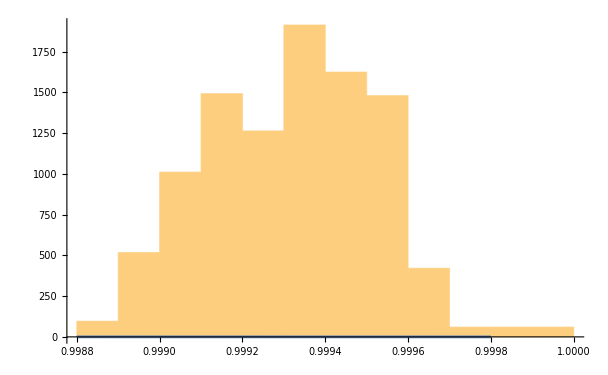

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[edist,x],{x,0.9988, 0.9998},PlotStyle->AbsoluteThickness]]
```

```mathematica
edist=EstimatedDistribution[divideSequence,BetaDistribution[α,β], MaxIterations->Infinity]
```

BetaDistribution[13020.3,8.84502]

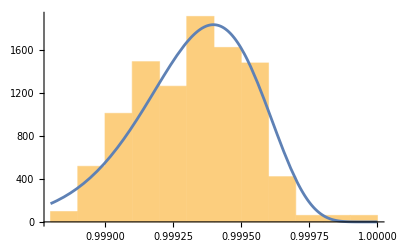

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[edist,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness]]
```

```mathematica
edistGamma=EstimatedDistribution[divideSequence,GammaDistribution[α,β], MaxIterations->Infinity]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {α} = {2.41922×10^7}. Try perturbing the initial point(s).

GammaDistribution[2.41922×10^7,4.13077×10^-8]

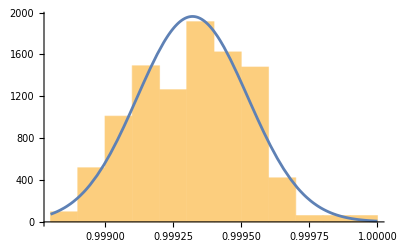

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[edistGamma,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness] ]
```

```mathematica
edistBeta=EstimatedDistribution[divideSequence,BetaDistribution[α,β], MaxIterations->Infinity]
```

BetaDistribution[13020.3,8.84502]

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[edistBeta,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness] ]
```

-Graphics-

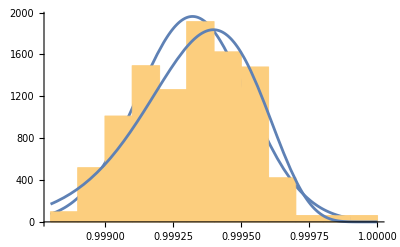

```mathematica
Show[%443, %445]
```

```mathematica
Import["/Users/miaanand/Downloads/download2.json", "Data"]//Normal
```

```mathematica
Values[%447][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]][[1]]
```

{value→579.20,qualifiers→{A},dateTime→2022-08-01T14:18:00.000-05:00}

```mathematica
ToExpression/@Table[Values[%447][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]][[n]][[1]][[2]], {n,1,Length@Values[%447][[4]][[2]][[2]][[1]][[3]][[2]][[1]][[1]][[2]]}]
```

```mathematica
Last@Sort@%487
```

579.99

```mathematica
Head[%491]
```

Real

```mathematica
divideSequence2 = %489/%491
```

```mathematica
edistBeta2=EstimatedDistribution[divideSequence,BetaDistribution[α,β], MaxIterations->Infinity]
```

BetaDistribution[13020.3,8.84502]

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[%496,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness]]
```

-Graphics-